```mathematica
Annihilation and g-2 Fit
```

```mathematica
Clear[Ml]
mu=0.105;
a = 3*^-9;
omega = 2.5*^-12;
Ncm = 1;
Ncq = 3;
mldiff = 200;
```

```mathematica
tfunc[m_,M_]:=m^2/M^2
d[m_]:=(11*tfunc[m,m+mldiff]^2-7*tfunc[m,m+mldiff]+2)/(18*tfunc[m,m+mldiff]-1)^3 -(tfunc[m,m+mldiff]^3*Log[tfunc[m,m+mldiff]])/(3*(tfunc[m,m+mldiff]-1)^4)
c[m_]:=(3*tfunc[m,m+mldiff]-1)/(4*(tfunc[m,m+mldiff]-1)^2) - (tfunc[m,m+mldiff]^2*Log[tfunc[m,m+mldiff]])/(2*(tfunc[m,m+mldiff]-1)^3)
p[g_,m_]:= g^2*mu^2/(16*Pi^2) * 1/(m+mldiff)^2
```

```mathematica
da[m_,g_]:=p[g,m]*(3/2*d[m]-c[m]) 
annDir[g_,m_,Nc_]:=Nc * g^4/(32*Pi*m^2) * 1/(1/tfunc[m,m+mldiff]+1)^2;
```

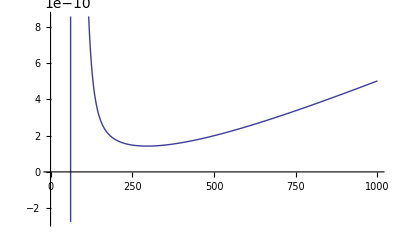

```mathematica
Plot[da[m,1.2],{m,0,1000}]
```

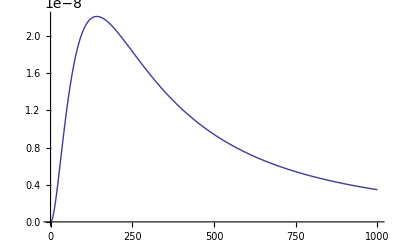

```mathematica
Plot[annDir[1.2,m,Ncm],{m,0,1000}]
```

```mathematica
annDir[1.,300,Ncm]
da[1,300]
```

5.97558×10^-8

2.87694×10^-9

```mathematica
Solve[annDir[g,M,Ncm] == omega && da[g,M]==a, {g,M}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(3125000 g^4)/(10000000200000001 M^2 π)==2.5×10^-12&&da[1/100000000,g,M]==3/1000000000,{g,M}]

## Gripaios g-2

```mathematica
cbar = c;
dbar = d;
c1[t_]:= -c[1/t]/t;
d1[t_]:=d[1/t]/t;
k[t_]:= c[t]+3/2*d[t];
kbar[t_]:= cbar[t]+3/2*dbar[t];
sigmaF[Q_,t_]:=Q*k[t];
sigmaB[Q_,t_]:=Q*kbar[t];
aGrip[t_, M_, qf1_, qf2_, qb1_, qb2_, mu_, g_]:= g^2/(6Pi^ 2
```